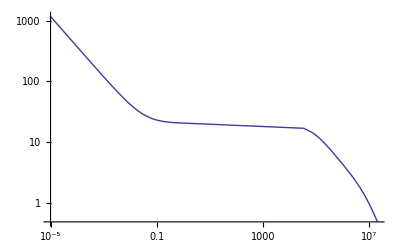

```mathematica
Clear["Global`*"];
SetDirectory["C:\\Users\\Documents\\n-ENDF-VII0.endf\\"];
NF=0;
callENDF[filename_]:=Module[{myline,zahler,XSHelastic},
EndfStream=OpenRead[filename];
myline="";XSHelastic={};
myline=Read[EndfStream,String];
zahler=0;
While[myline≠"EndOfFile",myline=Read[EndfStream,String];
If[myline≠"EndOfFile",
XSHelastic=Append[XSHelastic,ImportString[myline,"CSV"][[1]]];
zahler=zahler+1;
]
];NF=zahler;XSHelastic
]

H001elastic=callENDF["n-001_H_elasticInt"];
ListLogLogPlot[H001elastic,Joined->True]
```

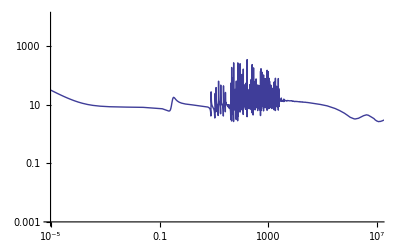

```mathematica
Pu094elastic=callENDF["n-094_Pu_239_elasticInt"];
Pu094inelastic=callENDF["n-094_Pu_239_inelasticInt"];
Pu094ngamma=callENDF["n-094_Pu_239_ngammaInt"];
Pu094fission=callENDF["n-094_Pu_239_fissionInt"];
Pu094total=callENDF["n-094_Pu_239_totalInt"];
ListLogLogPlot[{Pu094elastic},Joined->True,PlotRange->{{10^-5,10^7},{10^-3,10^4}}]
```

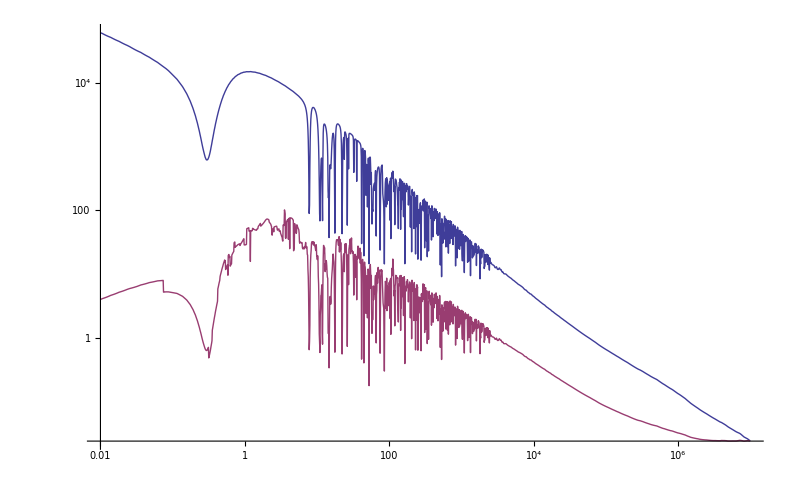

```mathematica
XSPuElastic=Interpolation[Pu094elastic,InterpolationOrder->1];
XSHElastic=Interpolation[H001elastic,InterpolationOrder->1];
XSPuTotal=Interpolation[Pu094total,InterpolationOrder->1];
XSPuAbsorb[e1_]:=XSPuTotal[e1]-XSPuElastic[e1];

escape[e1_]:=NIntegrate[XSPuAbsorb[e2]/(e2*(XSPuAbsorb[e2]+XSHElastic[e2])),{e2,e1,10^7}];
phis[e1_]:=10^6/((XSPuAbsorb[e1]+XSHElastic[e1])*e1)*Exp[-1*escape[e1]];
phist[e1_]:=10^6/((XSPuAbsorb[e1]+XSHElastic[e1])*e1);
LogLogPlot[{phist[s],phis[s]},{s,10^-2,10^7},PlotRange->All,PlotPoints->1000,MaxRecursion->1]
```

NIntegrate::nlim: e2 = s is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e2 near {e2} = {-0.0095271086982648967023123987019062042236328125}. NIntegrate obtained -20.8227 and 25.7267 for the integral and error estimates.

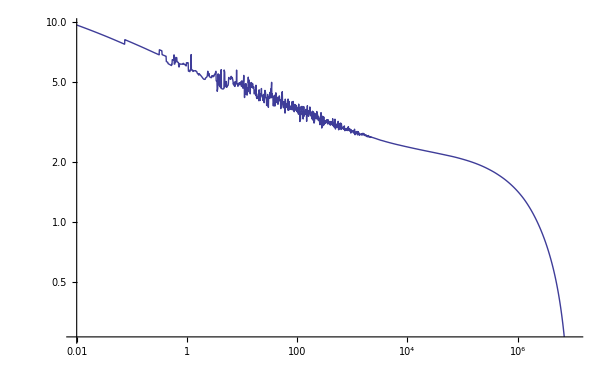

```mathematica
LogLogPlot[{escape[s]},{s,10^-2,10^7},PlotRange->All,PlotPoints->1000,MaxRecursion->1]
```